```mathematica
σ0N=120.;
s0=4m0[N938]^2;
A=0.050;
B=0.6;
ClearAll[σAnnp];ClearAll[σTotp];ClearAll[σElp];ClearAll[σDiffp];
σAnn[eCM_]:=σ0N * (s0/eCM^2)*(A^2 s0/((eCM^2-s0)^2+A^2 s0)+B);
σAnnp[p_]:=Block[{s=.938^2+.938^2+2 .938 Sqrt[p^2+.938^2]},
σ0N * (s0/s)*(A^2 s0/((s-s0)^2+A^2 s0)+B)
];
σTotp[p_]:=
Piecewise[{
{0.,p≤0.},
{271.6Exp[-1.1p^2],0<p≤0.3},
{75.0146+43.1276/p+2.58298/p^2-3.90783p,0.3≤ p<5.}
},38.4+77.6p^-0.64+0.26Log[p]^2-1.2Log[p]
];
σElp[p_]:=
Piecewise[{
{0.,p≤0.},
{78.6,0<p≤0.3},
{31.6+18.3/p-1.1/p^2-3.8p,0.3≤ p<5.}
},10.2+52.7p^-1.16+0.125Log[p]^2-1.28Log[p]
];
σDiffp[p_]:=σTotp[p]-σAnnp[p]-σElp[p];
```

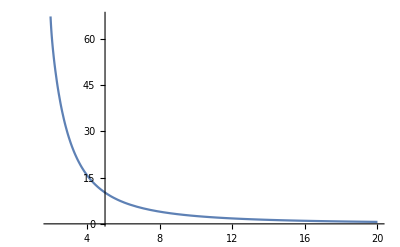

```mathematica
Plot[σAnn[eCM],{eCM,2,20}, PlotRange->All]
```

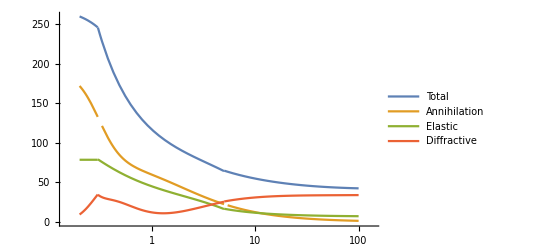

```mathematica
LogLinearPlot[{σTotp[p],σAnnp[p],σElp[p],σDiffp[p]},{p,.2,100.},PlotRange->{0,All},PlotLegends->{"Total","Annihilation","Elastic","Diffractive"}]
```